```mathematica
Needs["Benchmarking`"];
BenchmarkReport[]
```

NotebookObject[ | MathematicaMark7 Report]

```mathematica
Integrate[t^2/(t^4+es^2),{t,0,Infinity}]
```

If[Im[(-1)^(1/4) √es]<0&&Im[(-1)^(3/4) √es]>0,-(ⅈ π)/(2 √2 √es),Integrate[t^2/(es^2+t^4),{t,0,∞},Assumptions→Im[(-1)^(1/4) √es]≥0||Im[(-1)^(3/4) √es]≤0]]

```mathematica
f=Simplify[%]
```

1/(4 √2 √es)(-2 ArcTan[1-(√2 t)/(√es)]+2 ArcTan[1+(√2 t)/(√es)]+Log[es-√2 √es t+t^2]-Log[es+√2 √es t+t^2])

```mathematica
f-(f/.t->0)
```

1/(4 √2 √es)(-2 ArcTan[1-(√2 t)/(√es)]+2 ArcTan[1+(√2 t)/(√es)]+Log[es-√2 √es t+t^2]-Log[es+√2 √es t+t^2])

```mathematica
f/.t->Infinity
```

1/(4 √2 √es)(-2 ArcTan[1+(-∞)/(√Sign[es])]+2 ArcTan[1+∞/(√Sign[es])]+Log[∞+-∞ √Sign[es]]-Log[∞+∞ √Sign[es]])

```mathematica
Simplify[%,es>0]
```

Indeterminate

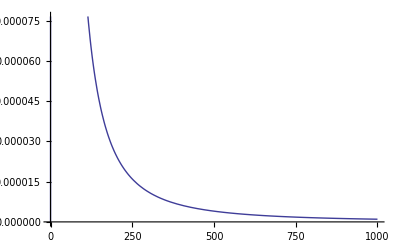

```mathematica
Plot[t^2/(t^4+es^2)/.es->10,{t,0,1000}]
```

```mathematica
h
```

```mathematica
ff[en_]:=(2en-R0)/((2en-R0)^2+R1^2);cond={R0->1,R1->0.1};cond2={R0->2,R1->1}
```

{R0→2,R1→1}

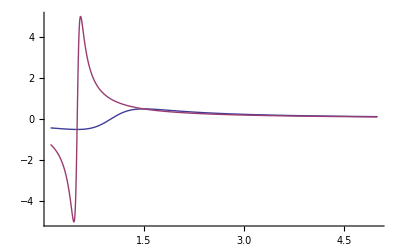

```mathematica
Plot[{(ff[en]/.cond2),(ff[en]/.cond)},{en,0.1,5},PlotRange->Full]
```

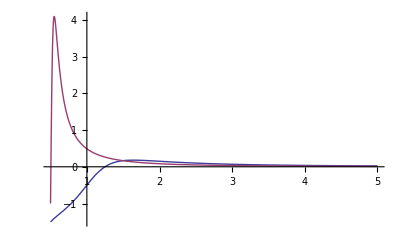

```mathematica
Plot[{(ff[en]/.cond2)-1/(2en),(ff[en]/.cond)-1/(2en)},{en,0.5,5},PlotRange->Full]
```

```mathematica
Integrate[(x)^(1/2)/(2x(2x-1)),x]
```

-ArcTanh[√2 √x]/(√2)

```mathematica
Simplify[%,x>1]
```

-ArcTanh[√2 √x]/(√2)

```mathematica
Series[ArcTanh[x],{x,
```

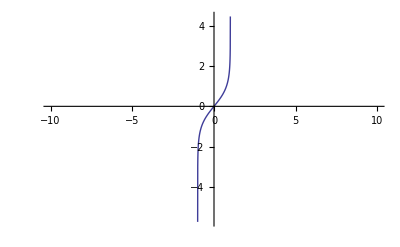

```mathematica
Plot[ArcTanh[x],{x,-10,10},PlotRange->Full]
```

```mathematica
N[ArcTanh[1000]]
```

0.001-1.5708 ⅈ

```mathematica
(x)^(1/2)/(2x(2x-1))
```

1/(2 √x (-1+2 x))

```mathematica
NIntegrate[(x-1-0.25)/(x^(1/2)((x-1)^2+0.25)),{x,100,Infinity}]
```

0.200501

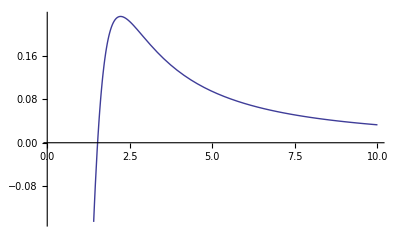

```mathematica
Plot[(x-1-0.525)/(x^(1/2)((x-1)^2+0.525)),{x,0.1,10}]
```